# Quadrature on Triangles

We want to be able to approximate integrals on triangles! Specifically we want to be able to evaluate integrals of polynomials exactly. This topic is called quadrature (or sometimes cubature) and is a very classical thing.

You already know something about this in 1D from calculus.

The Trapezoid rule is exact on Linear Functions.

Simpson’s rule is designed to be exact on quadratics and is accidentally exact on cubics.

## 1D Quadrature Rules

We have an interval a<x<b  and a polynomial p[x] of degree d and we want to approximate 
	∫_a^b p(x) dx = ∑_(i=1)^n ω_i p[x_i]
If we decide that we decide before hand that we want to use a fixed set of points x_i (which had better be in [a,b]) then we have n unknowns ω_i to choose.  This means we can select n linear conditions to enforce.

We are going to look at
	∫_0^1 p(x) dx = ∑_(i=1)^n ω_i p[x_i]
first and explain how to do other intervals later:  it is not a big deal!

### I=[0,1] and x_1=0 and x_2=1.

I have two constants to compute:  ω_1 and ω_2.  I can make the integral exact on two basis functions:  it makes sense to do 1 and x

```mathematica
fs={1,x};
xs = {0,1};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}]
Solve[QuadratureEquations]
```

{1==ω[1]+ω[2],1/2==ω[2]}

{{ω[1]→1/2,ω[2]→1/2}}

We just rediscovered the Trapezoid rule!

### I=[0,1] and x_1=1/2 and x_2=2/3.

I have two constants to compute:  ω_1 and ω_2.  I can make the integral exact on two basis functions:  it makes sense to do 1 and x

```mathematica
fs={1,x};
xs = {1/3,2/3};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}]
Solve[QuadratureEquations]
```

{1==ω[1]+ω[2],1/2==ω[1]/3+(2 ω[2])/3}

{{ω[1]→1/2,ω[2]→1/2}}

We just discovered a new rule!

### I=[0,1] and xs={0,1/2,1}

I have three constants to compute:  ω_1 and ω_2 and ω_3.  I can make the integral exact on three basis functions:  it makes sense to do 1 and x and x^2

```mathematica
fs={1,x,x^2};
xs = {0,1/2,1};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}]
Solve[QuadratureEquations]
```

{1==ω[1]+ω[2]+ω[3],1/2==ω[2]/2+ω[3],1/3==ω[2]/4+ω[3]}

{{ω[1]→1/6,ω[2]→2/3,ω[3]→1/6}}

We just rediscovered Simpson’s rule!

### I=[0,1] and xs={0,1/4,1/2,3/4,1}

It makes sense to do fs={1,x,x^2,x^3,x^4}

```mathematica
fs={1,x,x^2,x^3,x^4};
xs ={0,1/4,1/2,3/4,1};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}];
Solve[QuadratureEquations]
```

{{ω[1]→7/90,ω[2]→16/45,ω[3]→2/15,ω[4]→16/45,ω[5]→7/90}}

All of these are easy to solve for.

### I=[0,1] and two “good” points

I want ∫_0^1 p(x) dx = ∑_(i=1)^2 ω_i p[x_i] where I am willing to let the “math” tell me what x_1 and  x_2 to use.  
I now have 4 unknowns ω_1, ω_2 along with x_1 and  x_2.  I can enforce four conditions!

```mathematica
fs={1,x,x^2,x^3};
xs ={x1,x2};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}]
Solve[QuadratureEquations]
```

{1==ω[1]+ω[2],1/2==x1 ω[1]+x2 ω[2],1/3==x1^2 ω[1]+x2^2 ω[2],1/4==x1^3 ω[1]+x2^3 ω[2]}

{{x1→1/6 (3+√3),x2→1/6 (3-√3),ω[1]→1/2,ω[2]→1/2},{x1→1/6 (3-√3),x2→1/6 (3+√3),ω[1]→1/2,ω[2]→1/2}}

I got two paired solutions:  They are the same if you interchange x_1↔x_2.  This is a Gaussian quadrature.  Yes Gauss did everything!

### I=[0,1] and three “good” points

I want ∫_0^1 p(x) dx = ∑_(i=1)^3 ω_i p[x_i] where I am willing to let the “math” tell me what xs to use.  
I now have 6 unknowns 3 ωs along with three xs.  I can enforce six conditions!

```mathematica
fs={1,x,x^2,x^3,x^4,x^5};
xs ={x1,x2,x3};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}];
NSolve[QuadratureEquations]
```

{{x1→0.5,x2→0.887298,x3→0.112702,ω[1]→0.444444,ω[2]→0.277778,ω[3]→0.277778},{x1→0.887298,x2→0.112702,x3→0.5,ω[1]→0.277778,ω[2]→0.277778,ω[3]→0.444444},{x1→0.112702,x2→0.887298,x3→0.5,ω[1]→0.277778,ω[2]→0.277778,ω[3]→0.444444},{x1→0.112702,x2→0.5,x3→0.887298,ω[1]→0.277778,ω[2]→0.444444,ω[3]→0.277778},{x1→0.887298,x2→0.5,x3→0.112702,ω[1]→0.277778,ω[2]→0.444444,ω[3]→0.277778},{x1→0.5,x2→0.112702,x3→0.887298,ω[1]→0.444444,ω[2]→0.277778,ω[3]→0.277778}}

I get six paired solutions.  This is a Gaussian quadrature.  Yes Gauss did everything!

### I=[0,1] and four “good” points

I want ∫_0^1 p(x) dx = ∑_(i=1)^4 ω_i p[x_i] where I am willing to let the “math” tell me what xs to use.  
I now have 8 unknowns 4 ωs and xs.  I can enforce 8 conditions! There are a lot of solutions with quite a few being complex!

```mathematica
fs={1,x,x^2,x^3,x^4,x^5,x^6,x^7};
xs ={x1,x2,x3,x4};
QuadratureEquations=Table[
Integrate[f,{x,0,1}]==Sum[ω[i]f/.x->xs⟦i⟧,{i,Length[xs]}],
{f,fs}];
G4Sol=NSolve[QuadratureEquations,Reals]
```

{{x1→0.669991,x2→0.930568,x3→0.330009,x4→0.0694318,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.173927},{x1→0.330009,x2→0.930568,x3→0.0694318,x4→0.669991,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.173927,ω[4]→0.326073},{x1→0.930568,x2→0.0694318,x3→0.330009,x4→0.669991,ω[1]→0.173927,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.326073},{x1→0.930568,x2→0.669991,x3→0.330009,x4→0.0694318,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.326073,ω[4]→0.173927},{x1→0.669991,x2→0.930568,x3→0.0694318,x4→0.330009,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.173927,ω[4]→0.326073},{x1→0.930568,x2→0.669991,x3→0.0694318,x4→0.330009,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.326073},{x1→0.330009,x2→0.669991,x3→0.930568,x4→0.0694318,ω[1]→0.326073,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.173927},{x1→0.330009,x2→0.0694318,x3→0.930568,x4→0.669991,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.173927,ω[4]→0.326073},{x1→0.0694318,x2→0.930568,x3→0.330009,x4→0.669991,ω[1]→0.173927,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.326073},{x1→0.669991,x2→0.330009,x3→0.0694318,x4→0.930568,ω[1]→0.326073,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.173927},{x1→0.330009,x2→0.930568,x3→0.669991,x4→0.0694318,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.173927},{x1→0.930568,x2→0.330009,x3→0.669991,x4→0.0694318,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.326073,ω[4]→0.173927},{x1→0.0694318,x2→0.930568,x3→0.669991,x4→0.330009,ω[1]→0.173927,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.326073},{x1→0.0694318,x2→0.669991,x3→0.330009,x4→0.930568,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.326073,ω[4]→0.173927},{x1→0.930568,x2→0.330009,x3→0.0694318,x4→0.669991,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.326073},{x1→0.0694318,x2→0.330009,x3→0.669991,x4→0.930568,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.326073,ω[4]→0.173927},{x1→0.669991,x2→0.0694318,x3→0.930568,x4→0.330009,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.173927,ω[4]→0.326073},{x1→0.669991,x2→0.330009,x3→0.930568,x4→0.0694318,ω[1]→0.326073,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.173927},{x1→0.930568,x2→0.0694318,x3→0.669991,x4→0.330009,ω[1]→0.173927,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.326073},{x1→0.330009,x2→0.0694318,x3→0.669991,x4→0.930568,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.173927},{x1→0.330009,x2→0.669991,x3→0.0694318,x4→0.930568,ω[1]→0.326073,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.173927},{x1→0.0694318,x2→0.669991,x3→0.930568,x4→0.330009,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.326073},{x1→0.669991,x2→0.0694318,x3→0.330009,x4→0.930568,ω[1]→0.326073,ω[2]→0.173927,ω[3]→0.326073,ω[4]→0.173927},{x1→0.0694318,x2→0.330009,x3→0.930568,x4→0.669991,ω[1]→0.173927,ω[2]→0.326073,ω[3]→0.173927,ω[4]→0.326073}}

I get 8 paired real solutions.  This is a Gaussian quadrature.  Yes Gauss did everything!

### Using a Quadrature Scheme

Pretty easy to use. Grab the numbers and plug them into the appropriate sum.

```mathematica
Clear[f,f]
f[x_]:= Sin[x+Cos[x]]
NIntegrate[f[x],{x,0,1}]
{xs,ωs}={xs,{ω[1],ω[2],ω[3],ω[4]}}/.G4Sol[[1]];
Sum[ωs⟦i⟧f[xs⟦i⟧],{i,1,Length[xs]}]
```

## 2D Quadrature Rules

The question is how does this work in 2D.  Well it pretty much works the same way.  We will do our reference triangle {{0,0},{1,0},{0,1}}.

Just like in 1D we can either pick points or let the math pick the points.

### Corners Only

If we want to pick the corners {{0,0},{1,0},{0,1}} then we have three weights and we can impose three conditions.  It make sense to make sure we integrate linear functions spanned by {1,X,Y} exactly

Our first equation is

```mathematica
F[1][{X_,Y_}]:=1
Integrate[F[1][{X,Y}],{X,0,1},{Y,0,1-X}]==ω1 F[1][{0,0}]+ω2 F[1][{1,0}]+ω3 F[1][{0,1}]
```

1/2==ω1+ω2+ω3

Our second equation is

```mathematica
F[2][{X_,Y_}]:=X
Integrate[F[2][{X,Y}],{X,0,1},{Y,0,1-X}]==ω1 F[2][{0,0}]+ω2 F[2][{1,0}]+ω3 F[2][{0,1}]
```

1/6==ω2

And our third equation is

```mathematica
F[3][{X_,Y_}]:=Y
Integrate[F[3][{X,Y}],{X,0,1},{Y,0,1-X}]==ω1 F[3][{0,0}]+ω2 F[3][{1,0}]+ω3 F[3][{0,1}]
```

1/6==ω3

Solving the equations we get ω_1=ω_2=ω_3=1/6 and we get a 2D “trapezoid” rule that
	∫_∇ f[{X,Y}]dA≈1/6(f[{0,0}]+f[{0,1}]+f[{1,0}])
Lets test it

```mathematica
f[{X_,Y_}]:=Cos[X+Y]+ X^2+ Y^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],1/6 ( f[{0.0,0}]+f[{0,1}]+f[{1,0}])}
```

{0.54844,0.680101}

Not too bad.

### Corners and Mid-Points

Suppose we are willing to use all the corners and all the mid points! This gives me six points with six weights and I can enforce six conditions!  Fortunately there are six linearly independent quadratic functions {1,X,Y,X^2,X Y,Y^2} in 2 dimensions!

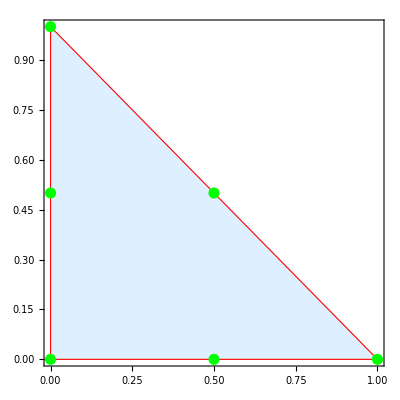

```mathematica
fs={1,X,Y,X^2,X Y,Y^2};
pts={{0,0},{1,0},{0,1},{0,1/2},{1/2,0},{1/2,1/2}};
Graphics[{
{EdgeForm[Red],LightBlue,Polygon[{{0,0},{1,0},{0,1}}]},
{Green, PointSize[0.02],Point[pts]}
},
Frame->True]
```

```mathematica
RHS=Table[ Integrate[f,{X,0,1},{Y,0,1-X}],{f,fs}]
M=Table[f/.{X->p⟦1⟧,Y->p⟦2⟧},{f,fs},{p,pts}];
MatrixForm[M]
ωs=LinearSolve[M,RHS]
```

{1/2,1/6,1/6,1/12,1/24,1/12}

(1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1/2 | 1/2
0 | 0 | 1 | 1/2 | 0 | 1/2
0 | 1 | 0 | 0 | 1/4 | 1/4
0 | 0 | 0 | 0 | 0 | 1/4
0 | 0 | 1 | 1/4 | 0 | 1/4)

{0,0,0,1/6,1/6,1/6}

We have just found out a scheme which only involves the mid points of the edges an apparently is exact on quadratics. Lets test it.  It is better than the corner one for sure.

```mathematica
f[{X_,Y_}]:= 1.1+Cos[X+Y]
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],1/6 ( f[{0.5,0}]+f[{0,0.5}]+f[{0.5,0.5}])}
```

{0.931773,0.932578}

It should be exact on any quadratic! Looks like it works!

```mathematica
f[{X_,Y_}]:= 1.2 + 2.3 X + 3.4 Y -0.8 X^2+0.1 X Y
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],1/6 ( f[{0.5,0}]+f[{0,0.5}]+f[{0.5,0.5}])}
```

{1.4875,1.4875}

```mathematica
f[{X_,Y_}]:= Cos[X+Y]+ X^2+ Y^2
{I1,I2}={NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],1/6 ( f[{0.5,0}]+f[{0,0.5}]+f[{0.5,0.5}])}
100 Abs[I1-I2]/I1
```

{0.54844,0.549245}

0.146709

### Corners and Third-Points

Suppose we are willing to use all the corners and all the third points and the “middle” third point. There are 10 such points.  There are 10 cubics in 2D!

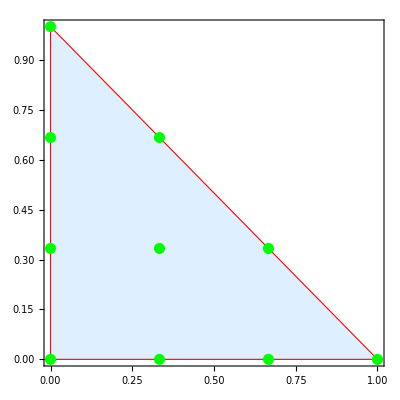

```mathematica
fs={1,X,Y,X^2,X Y,Y^2,X^3,X^2 Y,X Y^2,Y^3};
pts={{0,0},{1,0},{0,1},{0,1/3},{0,2/3},{1/3,0},{2/3,0},{1/3,2/3},{2/3,1/3},{1/3,1/3}};
Graphics[{
{EdgeForm[Red],LightBlue,Polygon[{{0,0},{1,0},{0,1}}]},
{Green, PointSize[0.02],Point[pts]}
},
Frame->True]
```

```mathematica
RHS=Table[ Integrate[f,{X,0,1},{Y,0,1-X}],{f,fs}];
M=Table[f/.{X->p⟦1⟧,Y->p⟦2⟧},{f,fs},{p,pts}];
MatrixForm[M];
ωs=LinearSolve[M,RHS]
```

{1/60,1/60,1/60,3/80,3/80,3/80,3/80,3/80,3/80,9/40}

We have just found out a scheme which involves all the third points. The weights on all the third points are equal while the middle point and the corners are different. Lets test it.  It is better than the corner one for sure.

```mathematica
f[{X_,Y_}]:= Cos[X+Y]+ X^2+ Y^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],
Sum[1.0ωs⟦i⟧ f[pts⟦i⟧],{i,Length[pts]}]}
```

{0.54844,0.548504}

It should be exact on any cubic! Looks like it works!

```mathematica
f[{X_,Y_}]:= 1.2 + 2.3 X + 3.4 Y -0.8 X^2+0.1 X Y + 1.2 X^3 - 3.2 X^2 Y
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],Sum[ωs⟦i⟧ f[pts⟦i⟧],{i,Length[pts]}]}
```

{1.49417,1.49417}

### Etc ...

Hopefully, it is sort of clear that you can keep playing this game of picking specific points and generating a quadrature that is correct on a bunch of functions!

### Undetermined Points

If we let the math pick the points we have more freedom!  I am going to go back to finding a quadrature that is accurate on the six quadratics and I am going to use the corners points and one extra point {X4,Y4} that I am going to let the math decide where to put it. I have 6 unknowns:  3 corner weights
{ω1,ω2,ω3}  along with the weight of the extra point ω4 and the 2 coordinate X4 and Y4 of the extra point.  The equations are NOT linear any more.

```mathematica
fs={1,X,Y,X^2,X Y,Y^2};
pts={{0,0},{1,0},{0,1},{X4,Y4}};
Eqs=Table[
Integrate[f,{X,0,1},{Y,0,1-X}]==Sum[ω[p]*f/.{X->p⟦1⟧,Y->p⟦2⟧},{p,pts}],
{f,fs}]
Solve[Eqs,
{ω[{0,0}],ω[{0,1}],ω[{1,0}],ω[{X4,Y4}],X4,Y4}
]
```

{1/2==ω[{0,0}]+ω[{0,1}]+ω[{1,0}]+ω[{X4,Y4}],1/6==ω[{1,0}]+X4 ω[{X4,Y4}],1/6==ω[{0,1}]+Y4 ω[{X4,Y4}],1/12==ω[{1,0}]+X4^2 ω[{X4,Y4}],1/24==X4 Y4 ω[{X4,Y4}],1/12==ω[{0,1}]+Y4^2 ω[{X4,Y4}]}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of FactorSquareFreeList[-1+24 ω[{0,0}]].

{{ω[{0,0}]→1/24,ω[{0,1}]→1/24,ω[{1,0}]→1/24,ω[{X4,Y4}]→3/8,X4→1/3,Y4→1/3}}

We have just found a scheme that involves the middle third point and the three corners.

```mathematica
Cos[X+Y]+ X^2+ Y^2
```

```mathematica
f[{X_,Y_}]:= Cos[X+Y]+ X^2+ Y^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],
1/24(f[{0,0}]+ f[{0,1}]+f[{1.,0}]) + 3/8 f[{1/3,1/3}]
}
```

{0.54844,0.548066}

It should be exact on any quadratic! Looks like it works!

```mathematica
f[{X_,Y_}]:= 1.2 + 2.3 X + 3.4 Y -0.8 X^2+0.1 X Y + 1.2 X^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],
1/24(f[{0,0}]+ f[{0,1}]+f[{1,0}]) + 3/8 f[{1/3,1/3}]}
```

{1.5875,1.5875}

## MidPoint

```mathematica
fs={1,X,Y};
pts={{X1,Y1}};
Eqs=Table[
Integrate[f,{X,0,1},{Y,0,1-X}]==Sum[ω[p]*f/.{X->p⟦1⟧,Y->p⟦2⟧},{p,pts}],
{f,fs}]
Solve[Eqs,
{ω[{X1,Y1}],X1,Y1}
]
```

{1/2==ω[{X1,Y1}],1/6==X1 ω[{X1,Y1}],1/6==Y1 ω[{X1,Y1}]}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of FactorSquareFreeList[-1+2 ω[{X1,Y1}]].

{{ω[{X1,Y1}]→1/2,X1→1/3,Y1→1/3}}

## Undetermined Points: Degenerate

If we let the math pick the points we have more freedom!  I am going to go back to finding a quadrature that is accurate on the six quadratics and I am going to use the edge points and one extra point {X4,Y4} that I am going to let the math decide where to put it. I have 6 unknowns:  3 corner weights
{ω1,ω2,ω3}  along with the weight of the extra point ω4 and the 2 coordinate X4 and Y4 of the extra point.  The equations are NOT linear any more.

```mathematica
fs={1,X,Y,X^2,X Y,Y^2};
pts={{1/2,0},{1/2,1/2},{0,1/2},{X4,Y4}};
Eqs=Table[
Integrate[f,{X,0,1},{Y,0,1-X}]==Sum[ω[p]*f/.{X->p⟦1⟧,Y->p⟦2⟧},{p,pts}],
{f,fs}];
Solve[Eqs,
{ω[{1/2,0}],ω[{1/2,1/2}],ω[{0,1/2}],ω[{X4,Y4}],X4,Y4}
]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of FactorSquareFreeList[-1+6 ω[{0,1/2}]+6 ω[{X4,Y4}]-12 X4 ω[{X4,Y4}]].

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ω[{1/2,0}]→1/6,ω[{1/2,1/2}]→1/6,ω[{0,1/2}]→1/6,ω[{X4,Y4}]→0},{ω[{1/2,0}]→1/6,ω[{1/2,1/2}]→1/6,ω[{0,1/2}]→1/6 (1-6 ω[{X4,Y4}]),X4→0,Y4→1/2},{ω[{1/2,0}]→1/6,ω[{1/2,1/2}]→1/6 (1-6 ω[{X4,Y4}]),ω[{0,1/2}]→1/6,X4→1/2,Y4→1/2},{ω[{1/2,0}]→1/6 (1-6 ω[{X4,Y4}]),ω[{1/2,1/2}]→1/6,ω[{0,1/2}]→1/6,X4→1/2,Y4→0}}

We have just found a scheme that involves the middle third point and the three corners.

```mathematica
Cos[X+Y]+ X^2+ Y^2
```

```mathematica
f[{X_,Y_}]:= Cos[X+Y]+ X^2+ Y^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],
1/24(f[{0,0}]+ f[{0,1}]+f[{1.,0}]) + 3/8 f[{1/3,1/3}]
}
```

{0.54844,0.548066}

It should be exact on any quadratic! Looks like it works!

```mathematica
f[{X_,Y_}]:= 1.2 + 2.3 X + 3.4 Y -0.8 X^2+0.1 X Y + 1.2 X^2
{NIntegrate[f[{X,Y}],{X,0,1},{Y,0,1-X}],
1/24(f[{0,0}]+ f[{0,1}]+f[{1,0}]) + 3/8 f[{1/3,1/3}]}
```

{1.5875,1.5875}